#### Animate frames with dislocations - runs slow due to inclusion of PlotMarkers

```mathematica
SetDirectory[NotebookDirectory[]];
jobdir="job1411479025-velpredict";
```

```mathematica
frames=Import[jobdir<>"//guidata.dat","List"][[3;;]];
Print["time: "<> ToString[ToExpression[frames[[-1]]][[1]]]];
Print["frame count: " <> ToString[Length[frames]]];
frames=ToExpression[StringReplace[#,{"e+":>"*^","e-":>"*^-"}]&/@frames][[;;,3;;]];

frames=frames[[;;,;;,{2,3,6}]];

frames5=(Select[#,#[[3]]==5&]&/@frames)[[;;,;;,{1,2}]];
(*frames6=(Select[#,#[[3]]==6&]&/@frames)[[;;,;;,{1,2}]];*)
frames7=(Select[#,#[[3]]==7&]&/@frames)[[;;,;;,{1,2}]];
framesOther=(Select[#,#[[3]]!=5&&#[[3]]≠7&]&/@frames)[[;;,;;,{1,2}]];

pins=Import[jobdir<>"//pinsdata.txt","Table"];
Print["Frames data generated."];
all=Transpose[{frames5,frames7,framesOther}];
"Frames data generated."
allplots=ListPlot[#,PlotMarkers->None,(* {▲,■,{●,Small}},*)PlotStyle-> {{Red,PointSize[Large]},{Blue,PointSize[Large]},Gray},ImageSize-> 800,AspectRatio->8*Sqrt[3/4]/60,PlotRange-> {{20,80},{0,8*Sqrt[3/4]}}]&/@all;
Print["ListPlots done."];

mov=ListAnimate[allplots,AnimationRate->40,AnimationRunning->True]
```

time: 21500

frame count: 215

Frames data generated.

Frames data generated.

ListPlots done.

```mathematica
SetDirectory[NotebookDirectory[]]
Export[jobdir<>"//frames.mov",allplots,"VideoEncoding"-> "Animation"]
```

C:\Users\jon\Dropbox\Uni\PhD\Research Topics\GND density

#### Frames with colour coded v_x velocity

```mathematica
frames=Import[jobdir<>"//guidata.dat","List"][[3;;]];
Print["time: "<> ToString[ToExpression[frames[[-1]]][[1]]]];
Print["frame count: " <> ToString[Length[frames]]];
frames=ToExpression[StringReplace[#,{"e+":>"*^","e-":>"*^-"}]&/@frames][[;;,3;;]];

frames=frames[[;;,;;,{2,3,4}]];
Print["Frames data processed"];
```

time: 1000000

frame count: 10000

Frames data processed

```mathematica
allplots=
ParallelTable[
Graphics[
Map[
(*ListPlot[#,PlotMarkers-> Automatic, ImageSize-> 800,AspectRatio->8*Sqrt[3/4]/60,PlotRange-> {{20,80},{0,8*Sqrt[3/4]}},PerformanceGoal->"Speed",ColorFunction->Function[{x,y,z},Blend[{Blue,Red},z]]]&*){Blend[{Blue,Red},#[[3]]/0.04],PointSize[0.01],Point[{#[[1]],#[[2]]}]} &,frames[[n]]
]
,Axes->True,ImageSize->800,AspectRatio->8*Sqrt[3/4]/60,PlotRange-> {{0,80},{-0.5*Sqrt[3/4],8.5*Sqrt[3/4]}}],{n,1,Length[frames]}];

Print["ListPlots done."];
```

ListPlots done.

```mathematica
mov=ListAnimate[allplots,AnimationRate->40,AnimationRunning->True]
```

#### V_x(y) profile

{«1»}

{{14.0444,0.31522,0.0451211},{37.6458,0.841483,0.0550681},{36.4233,1.72943,0.0586059},{36.3737,5.19527,0.0588161},{35.7982,3.46215,0.0558218},{35.9217,2.60547,0.0575606},{13.7037,6.61564,0.0399837},{37.8741,6.09178,0.0577619},{36.0446,4.32866,0.0579613},{0.725134,-0.886295,-0.0959878},{0.424491,7.82515,0.0229899},{0.47986,-1.2996,-0.0016031}}

{{-1.2996,-0.0016031},{-0.886295,-0.0959878},{0.31522,0.0451211},{0.841483,0.0550681},{1.72943,0.0586059},{2.60547,0.0575606},{3.46215,0.0558218},{4.32866,0.0579613},{5.19527,0.0588161},{6.09178,0.0577619},{6.61564,0.0399837},{7.82515,0.0229899}}

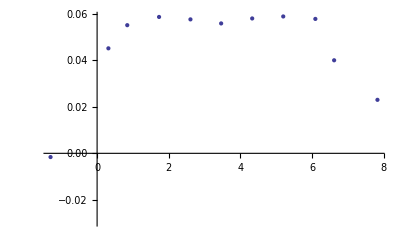

```mathematica
gath=GatherBy[Flatten[frames[[1000;;]],1],Round[#[[2]]/Sqrt[3/4]]&]
Mean[#]&/@gath
Sort[%[[;;,{2,3}]],#1[[1]]<#2[[1]]&]
ListPlot[%]
```